#### Function Testing (Working v1.1)

```mathematica
ArrayPlot[CellularAutomaton[{746,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{Table[1,{7}]},0},{{{150}}}],ImageSize->Tiny]
```

-Graphics-

```mathematica
cellularAutomata3DGraphicGenerator[cellularAutomataArray_/;MatrixQ[cellularAutomataArray],height_]:=(cellularAutomataPoints=Table[Flatten[(Function[{x},{{#,x}}&/@(Flatten@Position[cellularAutomataArray[[x]],i])]/@Range@Length@cellularAutomataArray),2],{i,DeleteDuplicates@DeleteCases[Flatten@cellularAutomataArray,0]}];pointList=Flatten[Function[{x},Append[#,x]&/@(Reverse[cellularAutomataPoints][[x]])]/@Range@Length@cellularAutomataPoints,1];translateHeight=Join[Drop[pointList//Transpose,{3}]//Transpose,List/@Table[height,Length@pointList],2];Graphics3D[{
Translate[Cuboid[{0,0,0},{1,1,pointList[[#,3]]}],translateHeight[[#]]]&/@Range@Length@pointList
},ImageSize->Large])
```

```mathematica
thing=Show[
cellularAutomata3DGraphicGenerator[CellularAutomaton[{746,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{Table[1,{7}]},0},{{{150}}}],1],
Graphics3D[{
Cuboid[{0,0,-2},{113,117,2}]
}],
cellularAutomata3DGraphicGenerator[CellularAutomaton[{746,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},{{Table[1,{7}]},0},{{{150}}}],-2]
]
```

-Graphics3D-

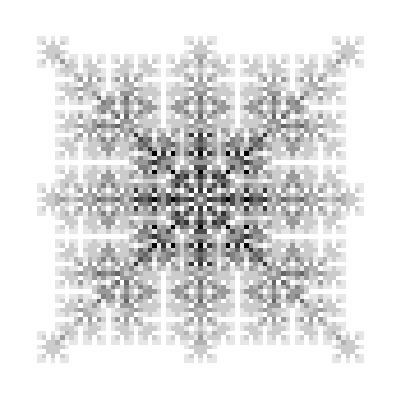

```mathematica
ArrayPlot[Mean[CellularAutomaton[{10, {2, 1}, {1, 1}},{{{1}},0},35]],ImageSize->Tiny]
```

```mathematica
cellularAutomata3DGraphicGenerator[Mean[CellularAutomaton[{10, {2, 1}, {1, 1}},{{{1}},0},35]]]
```

-Graphics3D-